### FindRoot - Broyden’s Method

<summary>
Helper method to calculate an approximation of the Jacobian.
< /summary >
< param name = "f" > The function. < /param >
< param name = "x0" > The argument (initial guess). < /param >
< param name = "y0" > The result (of initial guess). < /param >

#### Calculate Approximate Jacobian

```mathematica
CalculateApproximateJacobian[f_,x0_,y0_]:=Module[
{dim,B,x,h,xj,y,i,j},
dim =Length[x0];
B=ConstantArray[0,{dim,dim}];
x=x0;

For[j=1,j≤ dim,j++,
h=Abs[x0[[j]]];
If[h==0,h=0.0001];

xj=x[[j]];
x[[j]]=xj+h;
y=f[x];
x[[j]]=xj;

For[i=1,i≤ dim,i++,
B[[i,j]]=(y[[i]]-y0[[i]])/h;
];
];
Return[B];
];
```

< summary > Find a solution of the equation f (x) = 0. < /summary >
< param name = "f" > The function to find roots from. < /param >
< param name = "initialGuess" > Initial guess of the root. < /param >
< param name = "accuracy" > Desired accuracy.The root will be refined until the accuracy or the maximum number of iterations is reached. < /param >
< param name = "maxIterations" > Maximum number of iterations.Usually 100. < /param >
< param name = "root" > The root that was found, if any.Undefined if the function returns false. < /param >
< returns > True if a root with the specified accuracy was found, else false. < /returns >

#### FindRoot

```mathematica
TryBroydenFindRoot[f_,initialGuess_, accuracy_, maxIterations_]:=Module[
{
x,y0,y,g,dx,xnew,ynew,gnew,B,g2,scale,root,dF,dB
},
x=initialGuess;

y0=f[initialGuess];
y=y0;
g=Norm[y];

B=CalculateApproximateJacobian[f,initialGuess,y0];

For[i=1,i≤ maxIterations,i++,
dx=-Inverse[B].y;
xnew=x+dx;
ynew=f[xnew];
gnew=Norm[ynew];

If[gnew>g,
g2=g*g;
scale=g2/(g2+gnew*gnew);
If[scale==0,scale=0.0001];

dx=scale*dx;
xnew=x+dx;
ynew=f[xnew];
gnew=Norm[ynew];
];

If[gnew<accuracy,
Return[{"Solution"->xnew,"Success"->True}];
];

dF=ynew-y;
dB=(dF-B.dx).(dx*1/(Norm[dx]^2));
B=B+dB;

x=xnew;
y=ynew;
g=gnew;
];
Print["Not Converge! Residue : "<>ToString[gnew]];
Return[{"Solution"->xnew,"Success"->False}];
];
```

#### Demo

```mathematica
F1[u_]:={u,1/5*u*u-10};
F2[v_]:={9,3}+v*{2,3};
EquaSet[x_]:=Module[
{x1,y1,x2,y2},
{x1,y1}=F1[x[[1]]];
{x2,y2}=F2[x[[2]]];
Return[{x1-x2,y1-y2}];
];
```

```mathematica
Ans="Solution"/.TryBroydenFindRoot[EquaSet,{0,0},0.00000001,100]
```

{0.349632,-4.32518}

{-5.4661×10^-10,1.79921×10^-9}

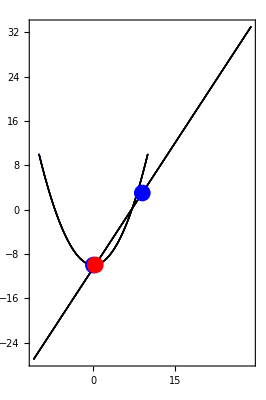

```mathematica
EquaSet[Ans]
Diagram1=ParametricPlot[{F1[u],F2[v]},{u,-10,10},{v,-10,10}];
AnsPlot=Graphics[{
Blue,PointSize-> 0.03,Point[F1[0]],
Blue,PointSize-> 0.03,Point[F2[0]],
Red,PointSize-> 0.03,Point[F1[Ans[[1]]]]
}];
Show[{Diagram1, AnsPlot}]
```

### Find Tangent Circle

#### Function

```mathematica
FindTangentCircle2D[curve1_,curveTangent1_,curve2_,curveTangent2_,initialCurvePara_]:=Module[
{
intersectionEqua,intersectionResult,intersectionPara,intersectionPoint,
TangentEqua
},
intersectionEqua[para_]:=Module[
{
p1,p2,delta,r,z
},
p1=curve1[para[[1]]];
p2=curve2[para[[2]]];
delta=p1-p2;
r=√(delta[[1]]^2+delta[[2]]^2);
z=delta[[3]];
Return[{r,z}];
];
(*求焦點*)
intersectionResult=TryBroydenFindRoot[intersectionEqua,initialCurvePara,10^-8,100];
If["Success"/.intersectionResult== False,
Return["Have no intersection point between two Curves."];
];
intersectionPara="Solution"/.intersectionResult;
intersectionPoint=curve1[intersectionPara[[1]]];

(*求相切圓*)
TangentEqua[]
];
```